# Unit 7 - Applications of the Derivative (2)

In Unit 7, we are to focus on optimization which is one typical and important application. Optimization is to find the extrema, i.e., the maximum and minimum values of a function. The first derivative test and the second derivative test are used to find local extrema. Over closed intervals, either test can be used to help find absolute extrema.

Topics covered in Unit 7 are listed below.

Review

Finding local and absolute extreme

Finding local extrema using FindMinimum and FindMaximum

Applications

## Review

The key concept here is critical number (or point). We call c a critical number of f(x) if f'(c)=0 or f'(c) does not exist.

We say f(c) is a local maximum (or minimum) value of f(x) if, for all x close to c, f(c)≥f(x) (or f(c)≤f(x)). We can prove that, if has a local maximum or minimum value at x=c, then f'(c)=0 or f'(c) does not exist; in other words, c is a critical number of f(x). Therefore, to find extrema of f(x), we always start from finding its critical numbers.

We say f(a) is an absolute maximum (or minimum) value of f(x) if, for all x in the domain of f(x), f(a)≥f(x) (or f(a)≤f(x)).

The first derivative test: If c is a critical point of f(x) and f is continuous at c, then (see the following two graphs),
(1) If f is strictly increasing on the near left of c , i.e., f'(x)>0, and strictly decreasing on the near right of c, i.e., f'(x)<0, f(c) is a local maximum value.
(2) If f is strictly decreasing on the near left of c, i.e., f'(x)<0, and strictly increasing on the near right of c, i.e., f'(x)>0, f(c) is a local minimum value.
(3) If f is always increasing (or decreasing) on both the near left and the near right of c, i.e., f'(x) keeps the same sign, f(c) is not a local extreme value.

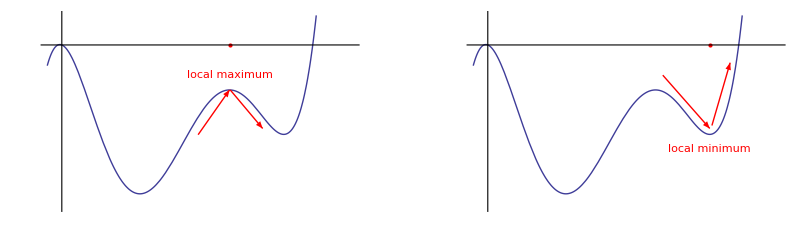

The second derivative test: Assume that f'(c)=0 and f''(c) exists.
(1) If f''(c)<0, i.e., f(x) is concave downward, f(c) is a local maximum.
(2) If f''(c)>0, i.e., f(x) is concave upward, f(c) is a local minimum.
(3) If f''(c)=0, it is inconclusive.

If f''(c) exists (and it is easy to compute), this test gives us greater convenience. However, the first derivative test is more general. If the second derivative test works, the first derivative test works, too. But the converse may not be true, i.e., if the first derivative test works, the second derivative test may not work.

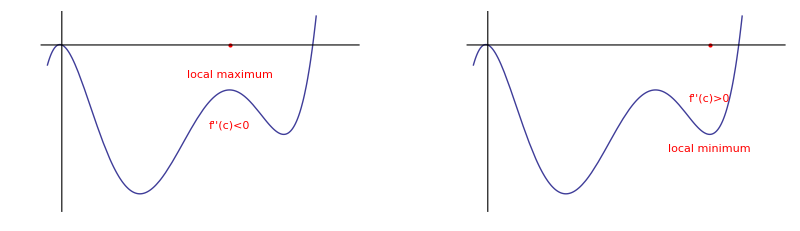

Finding absolute extrema on [a,b]: A continuous function f(x) attains its absolute extrema either at critical points or at the endpoints of the closed interval. Thus, we take three steps in order as follows.
(1) Find all critical points c_1,c_2,⋯, c_n,
(2) Evaluate f(x) at a,c_1,c_2,⋯,c_n,b
(3) The largest (or smallest) of these numbers is the absolute maximum (or minimum) value of f(x).

## Finding local and absolute extrema

Example 1
Use the first derivative test to find the local extrema of f(x)=x^4+2 x^3-3 x^2+2.

First, find all critical points.

```mathematica
f[x_]:=x^4+2x^3-3x^2+2
cps=x/.NSolve[f'[x]==0,x,Reals]
```

{-2.18614,0,0.686141}

```mathematica
f[%]
```

{-10.3928,2,1.45533}

The three critical points separate (-∞,∞) into four subintervals, (-∞,-2.18614), (-2.18614,0), (0,0.686141), and (0.686141,∞). Choose an “easy” number on each subinterval and evaluate f'.

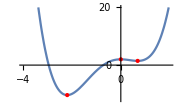

```mathematica
Show[{
Plot[f[x],{x,-4,2},PlotRange->{-12,20},ImageSize->180],
Table[Graphics[{Red,PointSize[Medium],Point[{cps[[i]],f[cps[[i]]]}]}],{i,1,Length[cps]}]}]
```

(-∞,∞) consists of multiple subintervals separated by critical points. One testing point is chosen on each subinterval.

```mathematica
f'[{-3,-2,0.5,1}](* evaluate f'(x) at each testing point *)
```

{-36,4,-1.,4}

Near the critical point x=-2.18614, f'(x) changes from negative to positive from left to right. Thus, f(-2.18614)=-10.3928 is a local minimum value of f(x).
Similarly, f(0)=2 and f(0.686141)=1.45533 are local maximum and local minimum values of f(x), respectively.

Example 2
Use the second derivative test to find the local extrema of f(x)=x^4+2 x^3-3 x^2+2.

First, find the critical points.

```mathematica
f[x_]:=x^4+2x^3-3x^2+2
cps=x/.NSolve[f'[x]==0,x,Reals]
```

{-2.18614,0,0.686141}

```mathematica
f[cps]
```

{-10.3928,2,1.45533}

Now, find f''(x) and evaluate it at each critical point.

```mathematica
f''[cps]
```

{25.1168,-6,7.88316}

Since f''(-2.18614)=25.1168>0, f(x) at the point is concave upward and, thus, f(-2.18614)=-10.3928 is a local minimum of f(x).
Similarly, by the second derivative test, Similarly, f(0)=2 and f(0.686141)=1.45533 are local maximum and local minimum values of f(x), respectively.

Example 3
Find the absolute extrema of f(x)=x^4+2 x^3-3 x^2+2 on [-2,2].

First, compute the critical points in the specified interval.

```mathematica
f[x_]:=x^4+2x^3-3x^2+2
cps=x/.NSolve[f'[x]==0&&-2≤x≤2,x]
```

{0.,0.686141}

Now, evaluate f(x) at each critical point and the two endpoints of the given closed interval.

```mathematica
xs=Sort[Flatten[{cps, -2,2}]]
```

{-2,0.,0.686141,2}

```mathematica
fValues=f[xs]
```

{-10,2.,1.45533,22}

```mathematica
Max[fValues]
```

22

```mathematica
Min[fValues]
```

-10

Thus, 22 and -10 are the absolute maximum and minimum values of f(x) on [-2,2], respectively.

Example 4
Write a Mathematica function that finds the absolute extrema of any polynomial function on a closed interval.

It is rather difficult to write a general Mathematica function that can find extrema of any given function f(x). It involves symbolic operations and rules for finding the domain of radical, rational, logarithmic, trigonometric functions or a function of their combination and composition because f(x) may have critical points where f'(x) does not exist. The task itself is a big project. But for polynomial functions, it will not be a big problem.

```mathematica
FindPolynomialAbsoluteExtrema[func_,{x_,a_,b_},plotQ_]:=Module[
{f,cps,xs,fValues,iMax,iMaxs, iMin,iMins,i},

f[X_]:=func/.x->X;
cps=x/.NSolve[f'[x]==0&&a≤x≤b,x];(* all critical points in [a, b] *)

(* evaluate f(x) at critical points as well as the endpoints of [a, b] *)
xs =Sort[ Flatten[{cps,a,b}]];
fValues=f[xs];

(* find absolute maximum values *)
iMax=1;
iMaxs = {1};(* there may be multiple points where f(x) has the absolute maximum value *)
Do[If[fValues[[i]]>fValues[[iMax]],iMax=i;iMaxs={i},
If[Abs[fValues[[i]]-fValues[[iMax]]]<10^-16,(* with floating point numbers, we cannot use fValues[i]==fValues[[iMax]] *)
iMaxs=Append[iMaxs,i]]],
{i,2,Length[xs]}];
Print["Absolute maximum value ",{fValues[[iMax]],Table[x->xs[[iMaxs[[i]]]],{i,1,Length[iMaxs]}]}];

(* find absolute minimum values *)
iMin=1;
iMins={1}; (* there may be multiple points where f(x) has the absolute minimum value *)
Do[If[fValues[[i]]<fValues[[iMin]],iMin=i;iMins={i},
If[Abs[fValues[[i]]-fValues[[iMin]]]<10^-16,(* with floating point numbers, we cannot use fValues[i]==f[iMax] *)
iMins=Append[iMins,i]]],
{i,2,Length[xs]}];
Print["Absolute minimum value ",{fValues[[iMin]],Table[x->xs[[iMins[[i]]]],{i,1,Length[iMins]}]}];

If[plotQ==True,
Show[{Plot[f[x],{x,a,b},ImageSize->180],
Table[Graphics[{Red,PointSize[Medium],
Point[{xs[[iMaxs[[i]]]],fValues[[iMaxs[[i]]]]}]}],{i,1,Length[iMaxs]}],
Table[Graphics[{Blue,PointSize[Medium],
Point[{xs[[iMins[[i]]]],fValues[[iMins[[i]]]]}]}],{i,1,Length[iMins]}]}]]]
```

Absolute maximum value {22,{x→2}}

Absolute minimum value {-10,{x→-2}}

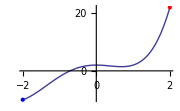

```mathematica
FindPolynomialAbsoluteExtrema[x^4+2x^3-3x^2+2,{x,-2,2},True]
```

The out put shows that f(x) attains its absolute maximum value 22 at x=2 and its absolute minimum value -10 at x=-2, on the interval [-2,2].

```mathematica
FindPolynomialAbsoluteExtrema[x^6-4x^3-3x+1,{x,-5,2},False]
```

Absolute maximum value {16141,{x→-5}}

Absolute minimum value {-6.87018,{x→1.3177}}

In fact, the code for FindPolynomialAbsoluteExtrema does not use any property specific to polynomial functions. It just assumes that there is no critical points at which f('x) does not exist. Therefore, we can apply it to any function differentiable on (a,b) and defined x=a and x=b. For example,

Absolute maximum value {7.91673,{x→-7.97867,x→7.97867}}

Absolute minimum value {-11.0407,{x→-11.0855,x→11.0855}}

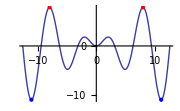

```mathematica
FindPolynomialAbsoluteExtrema[x Sin[x],{x,-4Pi,4Pi},True]
```

Absolute maximum value {1.30762,{x→1.8366}}

Absolute minimum value {-2.18277,{x→4.81584}}

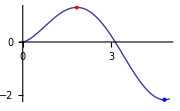

```mathematica
FindPolynomialAbsoluteExtrema[√x Sin[x],{x,0,5},True]
```

The Mathematica built-in function Do has similar usage like Table. It is not for generating a list. Instead, it is one way to execute a command repeatedly for certain number of times.

Usage:
(1) Do[command,{i_max}] is equivalent to Do[command,{i,1,i_max,1}]
(2) Do[command,{i,i_min,i_max}] is equivalent to Do[command,{i,i_min,i_max,1}] 
(3) Do[command,{i,i_min,i_max,di}] executes command with the variable i successively taking on the values i_min through i_max (in steps of di). 
(4) Do[command,{i,{i_1,i_2,…}}] executes command with the variable i successively taking on the values i_1,i_2,…
(5) Do[command,{i,i_min,i_max},{j,j_min,j_max},…]
If command consists of a sequence of commands, like with Module (see Unit 4), we either use a list of commands or use semicolon ( ; ) to separate commands.

Other basic functions for repeatedly executing a command for multiple times include For and While. Please refer to the Wolfram Documentation for more information.

```mathematica
Do[Print["Hello"],{2}] (* print Hello twice *)
```

Hello

Hello

```mathematica
primes ={2,3,5,7,11,13,17,19,23,29};
Do[Print[primes[[i]]],{i,3}] (* print the first 3 elements of the list primes *)
```

2

3

5

```mathematica
Do[Print[primes[[i]]],{i,2,8,2}] (* print the 2nd, 4th, 6th, and 8th elements of the list *)
```

3

7

13

19

```mathematica
(* find the sum of i1+2+3+⋯+100 *)
sum=0;
Do[sum+=i,{i,1,100}] (* x++ stands for x=x+1; x+=i stands for x=x+i. similarly, we have x-- and x-=i *)
sum
```

5050

For many tasks, we can use list and built-in functions to complete more efficiently. Do, For, and While just provide extra recourse for us to get things done. But if commands are executed repeatedly for multiple times under complicated conditions, these functions, especially, While, might be the only choice we may have.

```mathematica
Sum[i,{i,100}]
```

5050

```mathematica
Total[Table[i,{i,100}]]
```

5050

```mathematica
Apply[Plus,Table[i,{i,100}]]
```

5050

The following example prints a 9 x 9 multiplication table. Without using Do, For, or While, we still can do it. For example, we may replace Do with Table. But we will have to add semicolon ( ; ) at the end of this Table command so as to stop unwanted output. From the view of computer programming, Do, For, or While are certainly a more natural choice in this case.

```mathematica
Do[
Apply[Print,
Table[
StringJoin[ToString[i],"×",ToString[j],"=",
If[i*j<10,StringJoin[ToString[i*j]," "],ToString[i*j]]," "],
{j,9}]],
{i,9}]
```

1×1=1  1×2=2  1×3=3  1×4=4  1×5=5  1×6=6  1×7=7  1×8=8  1×9=9

2×1=2  2×2=4  2×3=6  2×4=8  2×5=10 2×6=12 2×7=14 2×8=16 2×9=18

3×1=3  3×2=6  3×3=9  3×4=12 3×5=15 3×6=18 3×7=21 3×8=24 3×9=27

4×1=4  4×2=8  4×3=12 4×4=16 4×5=20 4×6=24 4×7=28 4×8=32 4×9=36

5×1=5  5×2=10 5×3=15 5×4=20 5×5=25 5×6=30 5×7=35 5×8=40 5×9=45

6×1=6  6×2=12 6×3=18 6×4=24 6×5=30 6×6=36 6×7=42 6×8=48 6×9=54

7×1=7  7×2=14 7×3=21 7×4=28 7×5=35 7×6=42 7×7=49 7×8=56 7×9=63

8×1=8  8×2=16 8×3=24 8×4=32 8×5=40 8×6=48 8×7=56 8×8=64 8×9=72

9×1=9  9×2=18 9×3=27 9×4=36 9×5=45 9×6=54 9×7=63 9×8=72 9×9=81

The next example finds a root of f(x) near -2, applying Newton’s method (see Unit 6). Here, how many times a command is executed is unknown, but when to stop is certain. We simply cannot use Table, NestList, or some other functions together with list operations to do the job. In reality, Do and For do not help either. While is the only choice.

Usage: While[condition,command], testing condition, then executing command, repetitively, until condition first gives False.

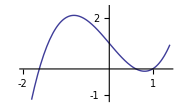

```mathematica
f[x_]:=x^3-2x+1
Plot[f[x],{x,-2,1.4},PlotRange->{-1.2,2.4},Ticks->{{-2,-1,1},{-1,1,2}},ImageSize->180]
newton[x0_]=x0-f[x0]/f'[x0]//N;
x0=-2;
While[Abs[f[x0]]>10^-16,x0=newton[x0]] (* see note *)
x0
```

Note: What is Abs[f[x0]]>10^-16? It is analytically f[x0]]≠0. But with computer floating numbers, we should not simply write x = y or x ≠ y. If we want to test if x = y, we had better write Abs[x-y]<10^-16 (or some other small tolerance); if we want to know if x ≠ y, we write Abs[x-y]>10^-16.

Example 5
Write a Mathematica function that finds the local extrema of any polynomial function.

See notes in Example 4.

```mathematica
FindLocalExtremaOfDifferentiableFunction[func_,{x_,a_,b_},plotQ_]:=Module[
{f,fPrime,fDPrime,cps,xs,i,xMaxs,xMins},

f[X_]=func/.x->X;
fPrime[X_]=D[f[X],X];
fDPrime[X_]=D[fPrime[X],X];

cps=x/.NSolve[fPrime[x]==0&&a<x<b,x,Reals];(* critical points *)

(* apply the second derivative test *)
xMaxs=Select[cps,fDPrime[#]<0&]; (* critical points where f(x) has local max value *)
xMins=Select[cps,fDPrime[#]>0&]; (* critical points where f(x) has local min value *)
Print["Local maximum values ", Table[{f[xMaxs[[i]]],{x->xMaxs[[i]]}},{i,1,Length[xMaxs]}]];
Print["Local maximum values ", Table[{f[xMins[[i]]],{x->xMins[[i]]}},{i,1,Length[xMins]}]];

If[plotQ==True,
Module[ {xmax,xmin},
xmin=If[a==-∞,Min[cps]-1,a];
xmax=If[b==∞,Max[cps]+1,b];
Show[{
Plot[f[x],{x,xmin,xmax},ImageSize->250],
Table[Graphics[{Red,PointSize[Medium],Point[{xMaxs[[i]],f[xMaxs[[i]]]}]}],{i,1,Length[xMaxs]}],
Table[Graphics[{Blue,PointSize[Medium],Point[{xMins[[i]],f[xMins[[i]]]}]}],{i,1,Length[xMins]}]
}]
]]
]

FindPolynomialLocalExtrema[func_,plotQ_] := FindLocalExtremaOfDifferentiableFunction[func,{x,-∞,∞},plotQ];
```

Local maximum values {{2,{x→0}}}

Local maximum values {{-10.3928,{x→-2.18614}},{1.45533,{x→0.686141}}}

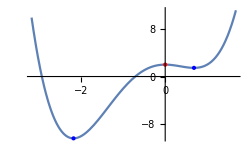

```mathematica
FindPolynomialLocalExtrema[x^4+2x^3-3x^2+2,True]
(* or FindLocalExtremaOfDifferentiableFunction[x^4+2x^3-3x^2+2,{x,-∞,∞},True] *)
```

```mathematica
FindPolynomialLocalExtrema[x^5-3x^4+2x^2+x-1,False]
```

Local maximum values {{0.179489,{x→0.81167}}}

Local maximum values {{-7.86873,{x→2.21927}}}

FindLocalExtremaOfDifferentiableFunction can find all local extrema of f(x) differentiable on (a,b).

Local maximum values {{14.1724,{x→-14.2074}},{7.91673,{x→-7.97867}},{1.81971,{x→-2.02876}},{1.81971,{x→2.02876}},{7.91673,{x→7.97867}},{14.1724,{x→14.2074}}}

Local maximum values {{-17.3076,{x→-17.3364}},{-11.0407,{x→-11.0855}},{-4.81447,{x→-4.91318}},{0.,{x→0.}},{-4.81447,{x→4.91318}},{-11.0407,{x→11.0855}},{-17.3076,{x→17.3364}}}

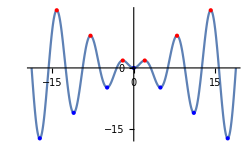

```mathematica
FindLocalExtremaOfDifferentiableFunction[x Sin[x],{x,-6Pi,6Pi},True]
```

Example 6
Find the absolute extrema of f(x)=(x^2+2x+1)/xon (0,∞).
Since the interval is open, we simply cannot take the steps for finding absolute extrema over a closed interval. But we may still take other approaches.

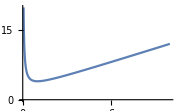

```mathematica
f[x_]:=(x^2+2x+1)/x
Plot[f[x],{x,0,10},PlotRange->{0,20},ImageSize->180]
```

The graph shows that there is one critical point where f'(x)=0.

```mathematica
NSolve[f'[x]==0&&x>0,x]
```

{{x→1.}}

x=1 is the one and only one critical point. Because

```mathematica
f''[1]
```

2

is positive, f(x) is concave upward on (0,∞). Therefore, f(1)=

```mathematica
f[1]
```

4

is the absolute minimum value over (0,∞).

There is no absolute maximum value, which can be confirmed by taking the limit of f(x) as x→0 and/or x→+∞.

## Finding local extrema using FindMaximum and FindMinimum

As we have seen in last section, it is rather difficult to develop a simple algorithm for find extrema of any function of general type. Mathematica provides two built-in functions, FindMaximum and FindMinimum, for searching for a LOCAL extreme value of a function. They work in a way quite similar to FindRoot.

Usage:

FindMaximum[f,x] searches for a local maximum in f, starting from an automatically selected point.

FindMaximum[f,{x,x_0}] searches for a local maximum in f, starting from the point x=x_0.

FindMaximum[{f,constraints},x}] searches for a local maximum in f subject to constraints, an automatically selected point.

FindMaximum[{f,constraints},{x,x_0}] searches for a local maximum in f subject to constraints, starting from the point x=x_0.

FindMinimum has same usage.

Both FindMaximum and FindMinimum can search for a local extreme values for multiple-variable functions. Please refer to the Wolfram Documentation for more information.

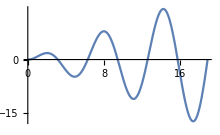

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.81971,{x→2.02876}}

{-4.81447,{x→4.91318}}

```mathematica
f[x_]:=x Sin[x];
Plot[f[x],{x,0,6Pi},ImageSize->220]
FindMaximum[f[x],{x,3}]
FindMinimum[f[x],{x,3}]
```

The output shows that these built-in functions take some numerical technique, covered by MATH 352, to locate local extrema. To hide extra information, call the built-in function Quiet.

```mathematica
FindMaximum[f[x],{x,3}]//Quiet
```

{1.81971,{x→2.02876}}

```mathematica
FindMaximum[f[x],x]
```

{1.81971,{x→2.02876}}

```mathematica
FindMaximum[{f[x],5≤x≤10},x]
```

{7.91673,{x→7.97867}}

```mathematica
FindMaximum[{f[x],5≤x≤10},{x,6}]
```

{7.91673,{x→7.97867}}

```mathematica
f[x_]:=(x-1)^2
FindMinimum[f[x],x]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.,{x→1.}}

Obviously, f(1)=0 is the one and only extreme value of the function. In Calculus II, you will learn concepts like saddle points.

## Applications

We are now to solve some applied optimization problems. We will first define a function to be maximized or minimized, and then apply the forgoing techniques to find its extreme value or how to get the extreme value.

The function may involve two or more variables originally. We will have to eliminate extra ones, via information presented or hidden in a problem, and make sure it is eventually a function of one variable, since the first and second derivative tests are both valid for single-variable functions only.

Example 7
A man wishes to use 100 feet of fencing to enclose a rectangular-shaped garden. What are the dimensions for the largest garden he can make with all of the fencing?

First, let x and y denote the width and the length (in feet) of the garden, respectively. The area of the garden is given by

A(x,y)=x y ⋯⋯⋯⋯⋯⋯⋯⋯ (1)

a two-variable function

Secondly, eliminate one of the two variables, either x or y, applying information presented in the problem. We know that the perimeter of the rectangle is

100=2(x+y), or x+y=50.

If we eliminate y in A(x,y)=x y, we express y in terms of x from the relation x+y=50 and obtain

y=50-x ⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)

Now, substitute (2) into (1) to obtain a single-variable function

A(x)=x(50-x) ⋯⋯⋯⋯⋯⋯⋯ (3)

The remaining part of the solution is to find the value of x and, thus, y via (2), such that A(x) is maximized.

```mathematica
A[x_]:=x(50-x)
x/.NSolve[A'[x]==0,x] (* critical points *)
```

{25.}

```mathematica
A''[%[[1]]] (* concavity *)
```

-2

This shows that x=25 is the only critical value and A(x) is concave downward. By the second derivative test, A(25)=625 is a local maximum value. In practice, it is also the absolute maximum value if we define the domain as [0,50] because, if x is beyond the range from 0 to 50, no rectangle can be formed with the 100-foot fencing .

Certainly, we can also simply use FindMaximum as follows.

```mathematica
FindMaximum[{A[x],0≤x≤50},x]
```

{625.,{x→25.}}

Therefore, the man can have a maximum garden of 626 square feet with each side of length 25 feet.

Example 8
The figure below shows a Norman window that has a shape of a rectangle surmounted by a semicircle. If the window has a perimeter of 30 feet, find its dimensions so that it allows the maximum amount of light to pass through.

Let x,y, and r denote the width, the height, and the radius of the semicircle of the window, respectively. To allow maximum amount of light through the window is to maximize the area of the windows. We know the area of the windows can be expressed in terms of x,y, and r as follows.

A(x,y,r)=1/2 π r^2+x y ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯(1)

Again, this is a multiple-variable function. We must first eliminate any two of the three variables, e.g., y and r. From the given conditions in the problem, we find

2r=x or r=1/2 x ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)

x+2y+1/2(2π r)=30 or x+2y+π r=30 ⋯⋯ (3)

From (2) and (3), we obtain

y=15-1/4(2+π)x ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯(4)

Substituting (2) and (4) into (1), we now define the area of the windows as a single-variable function A(x).

In addition, the domain of A(x) is [0,15]. Why? Commonsense tells that x≥0 and 2x=x+x≤x+1/2 π r≤30.

```mathematica
rRule=Solve[2r==x,r][[1]]//Simplify;
yRule = Solve[x+2y+1/2(2π r)==30,y][[1]]/.rRule//Simplify;
```

```mathematica
A[x_]=1/2 π r^2+x y/.rRule/.yRule//Simplify
```

-1/8 x (-120+(4+π) x)

```mathematica
cps=x/.NSolve[A'[x]==0 &&0≤x≤15,x] (* critical points *)
```

{8.40149}

Commonsense tells us that x≥0 and 2x≤30, or x∈[0,15]. We can evaluate A(x) at the two endpoints of the interval,

```mathematica
A[Flatten[{0,15,cps}]]//N
```

{0.,24.1427,63.0112}

Therefore, A(x)=63.0112 is the absolute maximum area of the window with the width of 8.40149 feet, the height of

```mathematica
y/.yRule /.x->cps[[1]]
```

4.20074

feet, and the radius of

```mathematica
r/.rRule/.x->cps[[1]]
```

4.20074

feet.

Example 9

A rectangle is contained in the region bounded by f(x)=2 sin x and the x-axis for 0≤x≤π. Find the dimensions of the largest rectangle.

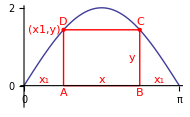

Let x and y denote the width and height of the rectangle, respectively. Thus, the area of the rectangle can be given by

A(x,y)=x y ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (1)

This is again a two-variable function. We must first eliminate one of the two variables, either x or y. Given that x_1 is the distance from the origin to point A, we know the distance from point B to point (π,0) is also x_1 due to the symmetric property of f(x) about x=π/2. Hence, x_1+x+x_1=π, or x_1=1/2(π-x).

Now, what is the value of y? Because points C and D are on the curve of f(x), y=f(x_1), using D, or y=f(x_1+x), using D. Due to the symmetric property of f(x) about x=π/2, f(x_1)=f(x_1+x). If you please, verify algebraically that f(x_1)=f(x_1+x). Let us just take

y=f(x_1)=f(1/2(π-x)) ⋯⋯⋯⋯⋯⋯⋯ (2)

Substitute (2) into (1), and obtain

A(x)=x f((π-x)/2) ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (3)

which is a single-variable function with the domain 0≤x≤π.

Now, let’s find the absolute maximum value of A(x) on [0,π].

```mathematica
f[x_]:=2Sin[x]
A[x_]=x f[(π-x)/2]//Simplify
```

2 x Cos[x/2]

```mathematica
APrime[x_]=A'[x]
```

2 Cos[x/2]-x Sin[x/2]

```mathematica
cps=x/.NSolve[APrime[x]==0&&0≤x≤π,x] (* find critical points *)
```

{1.72067}

Now, evaluate A(x) at critical points plus the endpoints of the interval.

```mathematica
A[{0,cp,π}]
```

{0,2.24439,0}

Therefore, the largest rectangle has the width of length

```mathematica
cp
```

1.72067

and the height of length

```mathematica
f[(π-x)/2]/.x->cp
```

1.30437

and the largest area is

```mathematica
A[cp]
```

2.24439

© 2015-2024 by David Wang, dwang@liberty.edu